# Differential Equation and Chaos Theory

Tianyi Wang

Eryn Gillam, Peter Barendse

Differential equations are widely used in math, physics, and engineering. These equations are very useful in modelling complex systems that are changing with time. For this exploration, the differential equations we are looking at have a particular form: x’’[t]+x’[t]==f[x[t]], where f is a real-valued function. The solutions exhibit a variety of different behaviors, some of which are stable, others chaotic. The goal of this project is to investigate different chaotic behaviors of these equations and to be able to detect them. Using supervised machine learning, we were able to classify different chaotic behaviors of differential equations.

## 1.Visualization of Chaotic Differential Equation

To get an idea of what a chaotic ODE looks like, we can generate plots for a few examples. The code plots the numerical solutions to different ODEs with the form we want to investigate.

```mathematica
Quiet[f[n_Integer]:=Part[x[t]//{Sin[#],Cos[#],Tan[#],Sec[#],Csc[#],Cot[#],Sinh[#],Cosh[#],Log[#],Exp[#],#^2}&,n];
Plot[#,{t,0,10},PlotRange->All]&/@Table[y=NDSolveValue[{x''[t]+x'[t]==f[n],x[0]==5,x'[0]==2},x[t],{t,0,10}],{n,1,11,1}]]
```

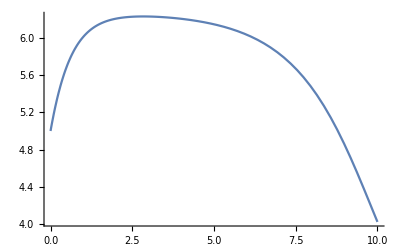
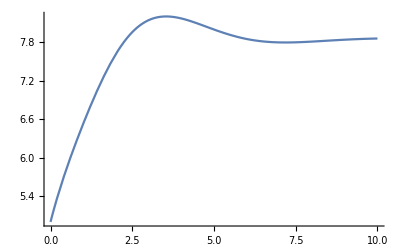
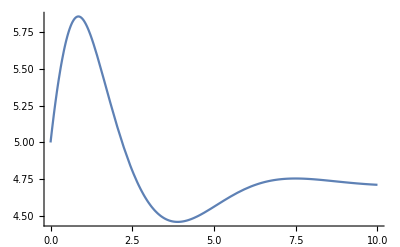
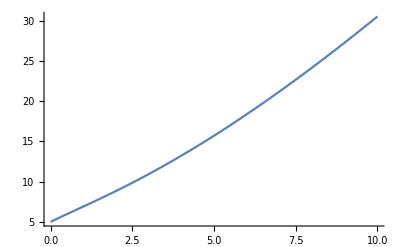
```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

As you can see, the 3rd, 4rd, 7th, and 9th graphs seem to exhibit chaotic behavior. They are chaotic because they are oscillating wildly in certain intervals. However, it doesn’t mean that the other ODEs are not chaotic- they may exhibit chaos if we change our plot range or initial conditions.

## 2.Phase Portrait Visualization

Another way to visualize the chaotic behavior of an ODE is through its phase portrait. A phase portrait shows how a solution x[t] to the ODE, its derivative, and its second derivative are changing as the independent variable (time, usually) changes. Here is an example that is POSSIBLY chaotic in range {t,0,15}:

This piece of code first solves the differential equation numerically, then generates a phase portrait in 3D space. y is the solution, Dy is its first derivative, and DDy is the second derivative.

```mathematica
y=NDSolveValue[{x''[t]+x'[t]==Sin[Exp[x[t]]],x[0]==2,x'[0]==3},x[t],{t,0,1000}];
Dy=D[y,t];
DDy=D[Dy,t];
Quiet[ParametricPlot3D[{y,Dy,DDy},{t,0,15},AxesLabel->{"y","Dy","DDy"},PlotRange->Automatic,PlotStyle->Gray]]
```

-Graphics3D-

The phase portrait visualizes the differential equation in 3D space. For this example, it is rotating around a specific point and finally converges, also evidenced by the following plot:

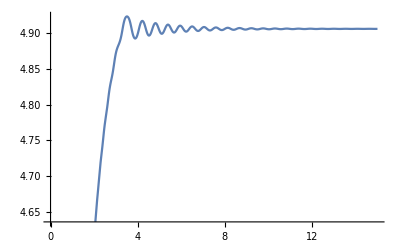

```mathematica
Plot[y,{t,0,15}]
```

We can also try to plot the phase portraits of all the functions from section 1.

```mathematica
Quiet[f[n_Integer]:=Part[x[t]//{Sin[#],Cos[#],Tan[#],Sec[#],Csc[#],Cot[#],Sinh[#],Cosh[#],Log[#],Exp[#],#^2}&,n];
Listy=Table[y=NDSolveValue[{x''[t]+x'[t]==f[n],x[0]==2,x'[0]==3},x[t],{t,0,10}],{n,1,11,1}];
ListDy=D[#,t]&/@Listy;
ListDDy=D[#,t]&/@ListDy;
Table[
ParametricPlot3D[{Listy[[n]],ListDy[[n]],ListDDy[[n]]},{t,0,10}],
{n,1,11,1}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Many of these portraits don’t seem to have graphs in them. The graphs are there, but since the volume of the rectangular space is very large compared to the graph, they are not visible. We have to search through these volumes to get visually distinguishable results.

plot and rasterize, and then detect the amount of red:

```mathematica
p=Rasterize@ParametricPlot3D[{x,x^3,1-x},{x,0,2},PlotStyle->{Red,Thick}]
Total@Flatten@ImageData@ColorDetect[p,Red]
```

-Graphics-

712.28

The code above uses the red color of the phase portrait to distinguish it. The code first rasterizes the graph, then returns a value for the intensity of red color. The algorithm searches through many possible ranges of one portrait, leaving the ones that are distinguishable based upon the red value, and discarding those that are not.

```mathematica
y=NDSolveValue[{x''[t]+x'[t]==Sin[Exp[x[t]]],x[0]==2,x'[0]==3},x[t],{t,0,1000}];
Dy=D[y,t];
DDy=D[Dy,t];
detectpic=Flatten@ParallelTable[Rasterize@ParametricPlot3D[{y,Dy,DDy},{t,0,2},
PlotStyle->{Red,Thick},PlotRange->{{0,r1},{0,r2},{0,r3}}],
{r1,0,10,5},{r2,0,10,5},{r3,0,10,5}];
redvalue=ParallelTable[Total@Flatten@ImageData@ColorDetect[detectpic[[n]],Red],
{n,1,Length[detectpic]}];
local=Flatten@Position[redvalue,_?(#≥700&)];
ParallelTable[detectpic[[local[[n]]]],{n,1,Length[local]}]
```

{-Graphics-,-Graphics-,-Graphics-}

In the code above, threshold red value is set to 700, which can vary for different functions. The threshold value leaves the picture with the amount of red above it and discards the rest. The graph suggests some complexity and chaos, however, it requires a lot of computational power. While parallel computing can be used, the step length must be set to be about 5 (in a range of 0-10) so that it computes in a reasonable amount of time. Therefore, a different method of computation is needed.

## 3.Euclidian Distance Test

Instead of looking for the phase portrait, we can calculate the distances between two points in phase portrait . Taking successive differences of sample points gives a sequence of distances. If the graph is chaotic, the distance between two successive points, will change drastically. The following code determines the interval on which the solution of x’’[t]+x’[t]==Sin[x[t]] looks chaotic:

```mathematica
y=NDSolveValue[{x''[t]+x'[t]==Sin[Exp[x[t]]],x[0]==2,x'[0]==3},x[t],{t,0,1000}];
Dy=D[y,t];
DDy=D[Dy,t];
```

vectorl produces the EuclideanDistance d_i=z(t_0)-z(t_0-Δ). disdiff produces 
the diffrences in distance ⅅ(i)=d_(i+1)-d_i, which happens in the interval(t_0,t_0+2Δ). If ⅅ(i)>N, then say the function is chaotic at the interval (t_0,t_0+Δ), which is just an approximation taking average
if ⅅ(i)=d_(i+1)-d_i>N, the function is chaotic at interval(t_0+(i-1)Δ,t_0+iΔ).

Euclidean distance between two points with time interval differences 1:

```mathematica
detectStableFixedEnding[f_,df_,ddf_, (*lasttime_:1000,*)t0_] := Module[{lengths},
	lengths = EuclideanDistance[{f, df, ddf}/.t->t0,{f, df, ddf}/.t->t0-1]];
```

all the distance

```mathematica
vectorl=ParallelTable[detectStableFixedEnding[y,Dy,DDy,n],{n,1,1000,1}];
```

differences of distances

```mathematica
disdiff=Table[Abs[vectorl[[n+1]]-vectorl[[n]]],{n,1,Length[vectorl]-1}];
```

The position where the differences >N or chaotic

```mathematica
chaospos=Flatten@Position[disdiff,_?(#>10^(-8)&)];
```

Time interval in which the function is chaotic.

```mathematica
list=Flatten@Table[{1+(chaospos[[n]]-1),1+chaospos[[n]]},{n,1,Length[chaospos]}];
```

```mathematica
list//.{x___,y_,y_,z___}:>{x,"~",z}
```

{1,~,80,81,~,267,268,269,270,~,272}

The output shows that the function is chaotic for the values of t {1, 80} , {81, 267} , {268}, {269}, and {270, 272}. However, this code does not work for the function x’’[t]+x’[t]==Exp[x[t]]. This is due to the computer failing to find values of the solution beyond t=300, while the code above searches the range {t, 0, 1000}.

```mathematica
Quiet[y=NDSolveValue[{x''[t]+x'[t]==Exp[x[t]],x[0]==2,x'[0]==3},x[t],{t,0,1000}];
Plot[y,{t,0,1000}]]
```

-Graphics-

## 4.Improvements

For some graphs, the range of phase portrait may be large, so the change between two successive points will also be fairly large. The relative difference can be used to describe the motion more accurately. This code is similar to section 3, but with a small change--instead of using distance differences, distance differences are divided by the distance of the vector to the origin.

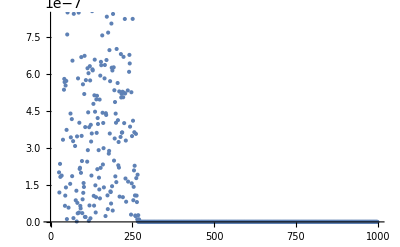

```mathematica
Quiet[y=NDSolveValue[{x''[t]+x'[t]==Sin[Exp[x[t]]],x[0]==2,x'[0]==3},x[t],{t,0,1000}];
Dy=D[y,t];
DDy=D[Dy,t];
detectStableFixedEnding[f_,df_,ddf_, (*lasttime_:1000,*)t0_] := Module[{lengths},
	length = EuclideanDistance[{f, df, ddf}/.t->t0,{f, df, ddf}/.t->t0-1]];
vectorl=Table[detectStableFixedEnding[y,Dy,DDy,n],{n,1,1000,1}];disdiffper=ParallelTable[(Abs[vectorl[[n+1]]-vectorl[[n]]])/Norm[{y,Dy,DDy}/.t->n],{n,1,Length[vectorl]-1}];
ListPlot[disdiffper]]
```

The function looks quite chaotic between range {t, 0, 300}, but as time goes on it become periodic. This suggests that the function is not chaotic -- instead, it only looks chaotic at low t values. This can be compared to the graph of the function:

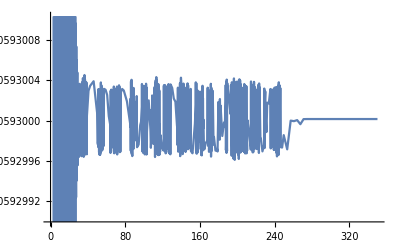

```mathematica
y=NDSolveValue[{x''[t]+x'[t]==Sin[Exp[x[t]]],x[0]==2,x'[0]==3},x[t],{t,0,1000}];
Plot[y,{t,0,350}]
```

The graph confirms the prediction, the function is chaotic at low t values and stabilizes for larger values of t.

## 5.Random ODE Generation and Local/Global Behavior Classification

Taking the algorithm in section 4, the chaotic behavior of random differential equation can be visualized. The following graphs are the result extracted from one thousand differential equations with the form x’’[t]+x’[t]==f[x[t]], taking the complexity of f to be 2 (a composition of functions) and 3 (a composition of compositions). 
	These graphs show can be subjectively classed into 10 classes of “behavior”, illustrated below by an example or two.

Pictures ( f )

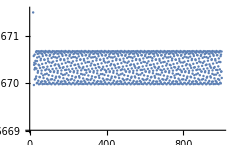
1--Graphics-Sin[x[t]]+1.2 x[t]

2--Graphics-Tan[x[t]]

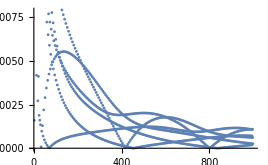
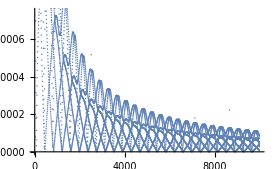
3--Graphics--Graphics-ⅇ^Cos[x[t]]

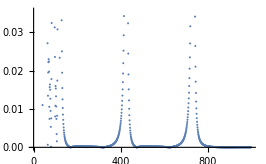
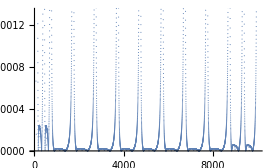
4--Graphics--Graphics--2x[t]

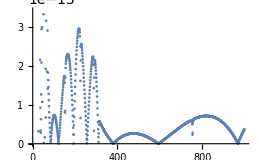
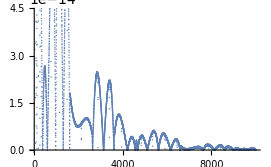
5--Graphics--Graphics-(-1000+x[t]) x[t]^x[t]

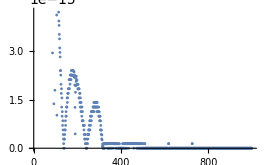
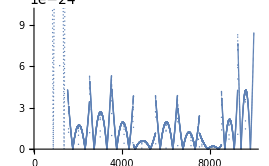
6--Graphics--Graphics--2 Sin[x[t]] x[t]

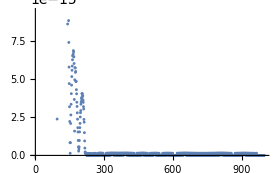
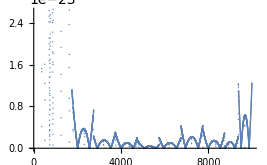
6--Graphics--Graphics-Sin[x[t]]

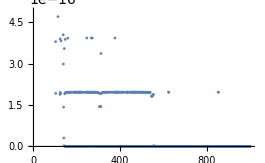
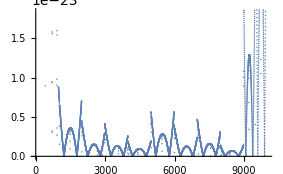
6--Graphics--Graphics-Cos[x[t]^2]

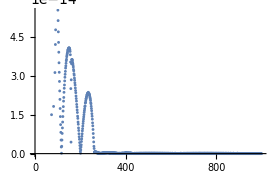
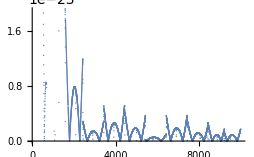
6--Graphics--Graphics-Cos[x[t]]

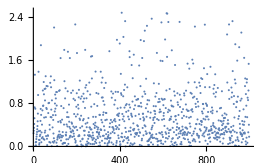
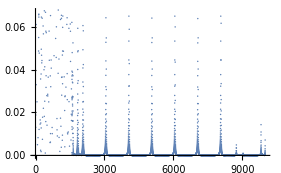
4--Graphics--Graphics--1000x[t]

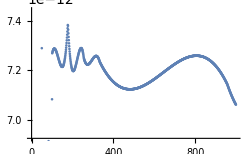
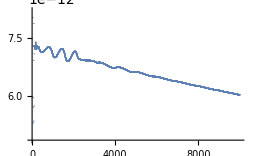
7--Graphics--Graphics-0.287301^(2 x[t])

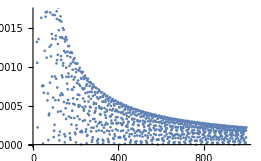
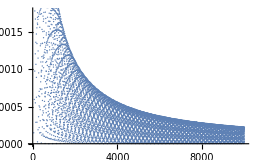
8--Graphics--Graphics-Cos[Sin[x[t]]]

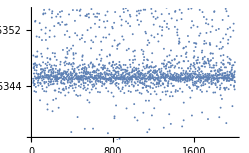
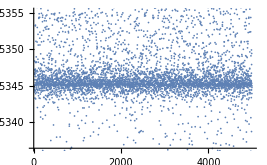
9--Graphics--Graphics-0.0854684 x[t]

## 6. Simplification and Machine Learning

The results of the simulations of these ODES were cleaned up and used in a machine learning to classify the chaotic behavior of different functions based on section 5.

The piece of code below puts the code in section 4 into a function, so it can be used more easily.

```mathematica
detectStableFixedEnding[f_,df_,ddf_, (*lasttime_:1000,*)t0_] := Module[{lengths},
	length = EuclideanDistance[{f, df, ddf}/.t->t0,{f, df, ddf}/.t->t0-1]];

makeVectFromFunc[q_, T_, a_, b_]:=Quiet[
y=NDSolveValue[{x''[t]+x'[t]==q,x[0]==a,x'[0]==b},x[t],{t,0,T}];
Dy=D[y,t];
DDy=D[Dy,t];

vectorl=Table[detectStableFixedEnding[y,Dy,DDy,n],{n,1,T,1}];disdiffper=Table[(Abs[vectorl[[n+1]]-vectorl[[n]]])/Norm[{y,Dy,DDy}/.t->n],{n,1,Length[vectorl]-1}]];
```

A training set is generated by changing the initial conditions of the functions in section 5 by a random amount. We make the assumption that this will not affect the subjective behavior class of its graph (which seems intuitively and empirically true), and so we label these with the same class label. The set is generated by classes and is compacted into one larger training set.

```mathematica
i=0;
class1ex=DeleteCases[Table[Print[i++];TimeConstrained[makeVectFromFunc[Sin[x[t]]+1.2 x[t], 1000,2+RandomReal[],3+RandomReal[]]->1
,1]
, {100}],$Failed];
```

```mathematica
i=0;
class2ex=DeleteCases[Table[Print[i++];TimeConstrained[makeVectFromFunc[Tan[x[t]], 1000,2+RandomReal[],3+RandomReal[]]->2
,1]
, {100}],$Failed];
```

```mathematica
i=0;
class3ex=DeleteCases[Table[Print[i++];TimeConstrained[makeVectFromFunc[Exp[Cos[x[t]]], 1000,2+RandomReal[],3+RandomReal[]]->3
,1]
, {100}],$Failed];
```

```mathematica
i=0;
class4ex=DeleteCases[Table[Print[i++];TimeConstrained[makeVectFromFunc[-2x[t], 1000,2+RandomReal[],3+RandomReal[]]->4
,1]
, {100}],$Failed];
```

```mathematica
i=0;
class5ex=DeleteCases[Table[Print[i++];TimeConstrained[makeVectFromFunc[(-1000+x[t]) x[t]^x[t], 1000,2+RandomReal[],3+RandomReal[]]->5
,1]
, {100}],$Failed];
```

```mathematica
i=0;
class6ex=DeleteCases[Table[Print[i++];TimeConstrained[makeVectFromFunc[Sin[x[t]], 1000,2+RandomReal[],3+RandomReal[]]->6
,1]
, {100}],$Failed];
```

```mathematica
i=0;
class7ex=DeleteCases[Table[Print[i++];TimeConstrained[makeVectFromFunc[0.28730050179405986^(2 x[t]), 1000,2+RandomReal[],3+RandomReal[]]->7
,1]
, {100}],$Failed];
```

```mathematica
i=0;
class8ex=DeleteCases[Table[Print[i++];TimeConstrained[makeVectFromFunc[Cos[Sin[x[t]]], 1000,2+RandomReal[],3+RandomReal[]]->8
,1]
, {100}],$Failed];
```

```mathematica
i=0;
class9ex=DeleteCases[Table[Print[i++];TimeConstrained[makeVectFromFunc[0.08546844325579328x[t], 1000,2+RandomReal[],3+RandomReal[]]->9
,1]
, {100}],$Failed];
```

Now let us put all classes into 1 training set and save it.

```mathematica
allclasses={class1ex,class2ex,class3ex,class4ex,class5ex,class6ex,class7ex,class8ex,class9ex};
DumpSave["allclasses.mx",allclasses];
```

There are some examples that are quite large and slow the machine down. These cases need to be removed.

```mathematica
allclasses=Select[2<ByteCount[#]<25000&]/@allclasses;
```

It is important to keep in mind that there may still be things we don’t want inside our data. Therefore, we want to delete $abort or $failed before training the machine.

```mathematica
cl=Classify[DeleteCases[Flatten[allclasses,1],$Aborted|$Failed]]
```

ClassifierFunction[…]

```mathematica
Information@cl
```

Classifier information
Data type | NumericalVector (length: 999)
Number of classes | 8
Accuracy | (99.00.8) %
Method | LogisticRegression
Single evaluation time | 26.7 ms/example
Batch evaluation speed | 232. examples/s
Loss | 0.0678 ± 0.023
Model memory | 656. kB
Training examples used | 776 examples
Training time | 8.48 s
 |

Though the accuracy seems to be 99%, it only indicates that the machine is doing well on the training set. Further testing is needed to determine how good the machine is. Therefore, a part of allclasses is removed from the training set (before training) to be used as a test set.

```mathematica
allclasses2=RandomSample[Flatten[allclasses,1]];
```

```mathematica
{test2,train2}={#[[;;100]],#[[101;;]]}&[allclasses2];
```

```mathematica
cl2=Classify[train2];
```

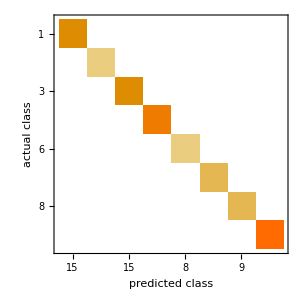

```mathematica
ClassifierMeasurements[cl2,test2,"ConfusionMatrixPlot"]
```

Though the accuracy is high, there are some graphs that have extremely small values. The machine may classify all the graphs with small number into one group. Multiplying the test set by a random real number gives a more accurate measure of the machine’s accuracy.

```mathematica
test3=(*Table[*)(RandomInteger[10000]  #[[1]]->#[[2]])&/@test2;
```

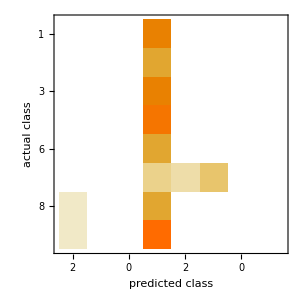

```mathematica
ClassifierMeasurements[cl2,test3,"ConfusionMatrixPlot"]
```

The machine’s actual accuracy is low, which confirms the problem with small values. The easiest fix is to multiply all the training set by a random real number as well.

```mathematica
train3=(*Table[*)(RandomInteger[10000]  #[[1]]->#[[2]])&/@train2;
cl3=Classify[train3]
```

ClassifierFunction[…]

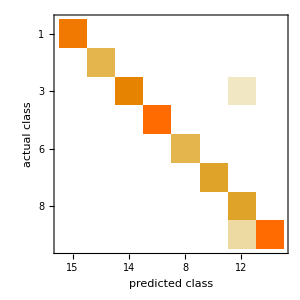

```mathematica
ClassifierMeasurements[cl3,test3,"ConfusionMatrixPlot"]
```

This time, the machine’s accuracy is high. The mistake is shown below.

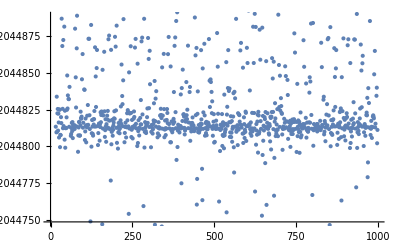

```mathematica
ListPlot@ClassifierMeasurements[cl3,test3,"MisclassifiedExamples"]
```

I did the two tests previously. The program made only one mistake as well. The misclassified examples is the following.

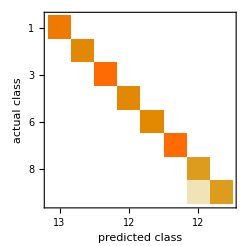
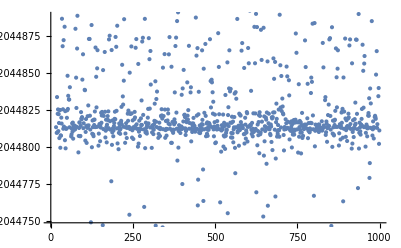

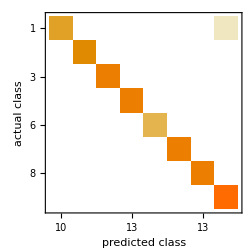
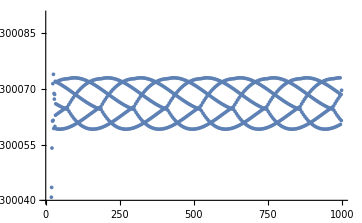

## 7.Theoretical Foundations

Theorem 1.  Assume the increment in time Δt >0, and the trajectory of an ordinary differential equation 𝔻(t) converges at point P. Then for all ϵ >0, there exists T_ϵ such that the |𝔻(t_(i+1))-𝔻(t_i)|< ϵ for all t_i>T_ϵ.
Proof.  Let {t_1,t_2,...,t_i,...} be any sequence such that t_i->0 as i->0. Choose any t_(i+1),t_i>T_(ϵ/2), then| 𝔻_(i+1)- P | <ϵ/2, |𝔻(t_i)-P|<ϵ/2.  Therefore, |𝔻(t_(i+1))-𝔻(t_i)|< ϵ for all t_i>T_ϵ. □

Theorem 2.  Let d_i=|𝔻(t_(i+1))-𝔻(t_i)| and let Δ_i=d_(i+1)-d_i. If Theorem 1. is true, then Δ_i<ϵ for all i>N.
Proof.  We already know that d_i=|𝔻(t_(i+1))-𝔻(t_i)|< ϵ for all t_i>T_ϵ, which means for all i>N. Therefore, d_(i+1)=|𝔻(t_(i+2))-𝔻(t_(i+1))|< ϵ. This shows that Δ_i=d_(i+1)-d_i< ϵ. □

## 8.Conclusions

Throughout this project, I successfully detected the chaotic behavior of different differential equations and classified them. The output includes a function that generates the phase portrait of some differential equations, and a function that tells the interval(s) in which the function is chaotic, for input functions (f[x]) that are continuous. Finally, there is a machine learned classifier function that can classify different behaviors of chaotic functions with accuracy about 99%-100%.